```mathematica
r=1;sigma=1;
p[s_]:=Piecewise[{{15-s,s<15},{0,s>15 }}];
c[s_]:=Piecewise[{{0,s<15},{s-15,s>15 }}]
```

```mathematica
f[s_]:=
```

```mathematica
V[S_,t_]:=Exp[r*t]/Sqrt[-t*2*Pi]*NIntegrate[Exp[(Log[S/s]+(r-sigma^2/2)(-t))^2/(2sigma^2t)]f[s]/s,{s,0,Infinity}]/sigma
```

```mathematica
Plot3D[V[S,t],{S,0,20},{t,-5,-0.01}]
```

-Graphics3D-

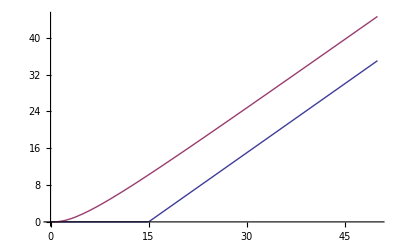

```mathematica
Plot[{f[S],V[S,-1.01]},{S,0,50},PlotRange->All]
```

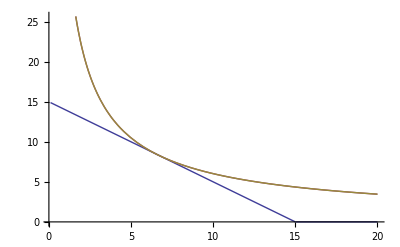

```mathematica
a=0.8;ss=15/(1+1/a);Plot[{p[s],(15-ss)(s/ss)^(-a),1/a*(15/(1+1/a))^(1+a)*s^{-a}},{s,0.1,20}]
```

```mathematica
D[1/a*(15/(1+1/a))^(1+a)*s^{-a},{s,2}]/.s->ss
```

{0.27}